```mathematica
Clear["Global`*"]
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
DelEle[list_,element_]:=Delete[list,FirstPosition[list,element]](* Delete Element *)
```

```mathematica
ListPosRef[list1_,list2_,element_]:=list1[[FirstPosition[list2,element][[1]]]](* list2でのelementの位置に来る、list1の要素を求める(list1にlist2の位置を反映 List Position Reflection) *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}]
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
RestMaxCurrEdgeNum[PartLoop_]:=(
For[i=1,
(Length[Complement[VertexList[{Ruleg[[SortCurr[[i]]]]}],VertexList[PartLoop]]]== 0|| Intersection[VertexList[PartLoop],VertexList[{Ruleg[[SortCurr[[i]]]]}]]== {}),
i++,];
SortCurr[[i]]
)
```

```mathematica
RestMaxCurrEdge[PartLoop_]:=Ruleg[[RestMaxCurrEdgeNum[PartLoop]]]
```

```mathematica
RestMaxCurrEdgeList[PartLoop_]:=VertexList[{RestMaxCurrEdge[PartLoop]}]
```

```mathematica
RestMaxCurrEdgeLoopSide[PartLoop_]:=Intersection[VertexList[PartLoop],RestMaxCurrEdgeList[PartLoop]][[1]]
```

```mathematica
RestMaxCurrEdgeRestSide[PartLoop_]:=DelEle[RestMaxCurrEdgeList[PartLoop],RestMaxCurrEdgeLoopSide[PartLoop]][[1]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,RestMaxCurrEdgeRestSide[PartLoop]]]]
```

```mathematica
InsertEdge[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]->RestMaxCurrEdgeRestSide[PartLoop],RestMaxCurrEdgeRestSide[PartLoop]->VertexList[{LoopDelEdge[PartLoop]}][[2]]}]]
```

### 入力

```mathematica
Pin=Table[{RandomReal[10],RandomReal[10]},{i,10}](*Point input*)
```

{{5.24681,9.61888},{1.13008,5.50347},{2.10773,8.65808},{0.554044,6.81158},{1.8326,6.08271},{7.15777,5.36764},{2.59896,5.81459},{3.67538,6.05457},{1.55453,5.18978},{7.17843,4.90225}}

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];(*Ggraph input*)
```

### 渦電流によるTSPの解法

```mathematica
AbsoluteTiming[
h=LoopMatrix[Gin];
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U);(* 誘導起電力行列を考慮した電流を求める式 *)
SortCurr=Reverse[Ordering[Abs[Curr]]];
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
]
```

{0.0515645,Null}

```mathematica
AbsoluteTiming[
MaxPartLoop={};
For[i=3,Length[MaxPartLoop]==0,i++,
MaxPartLoop=FindCycle[
Graph[EdgeList[Gout][[Reverse[Ordering[Abs[Curr]]][[Range[i]]]]]],
Infinity,All];
];
MaxPartLoop=EdgeRules[MaxPartLoop[[1]]];
Clear[InsertPartLoop];
InsertPartLoop={MaxPartLoop};
For[j=1,Complement[VertexList[Gin],VertexList[InsertPartLoop[[j]]]]≠{},j++,
InsertPartLoop=Append[InsertPartLoop,InsertEdge[InsertPartLoop[[j]]]]
];
]
```

{0.227084,Null}

```mathematica
EdgeSolution=Last[InsertPartLoop]
```

{10→6,6→1,1→3,3→4,4→2,2→9,9→5,5→7,7→8,8→10}

```mathematica
VertexSolution={1};
For[j=1,Length[VertexSolution]≠ Length[EdgeSolution],j++,
VertexSolution=Append[VertexSolution,EdgeSolution[[FirstPosition[EdgeSolution,VertexSolution[[j]]->_][[1]],2]]]
]
VertexSolution
```

{1,3,4,2,9,5,7,8,10,6}

```mathematica
Total[EdgeDList[EdgeSolution]]
```

19.3177

### mathematicaの関数によるTSPの解

```mathematica
AbsoluteTiming[FindShortestTour[Pin]]
MathematicaSolution=%[[2]];
```

{0.0233351,{19.3177,{1,6,10,8,7,5,9,2,4,3,1}}}

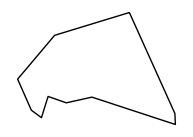

```mathematica
Graphics[Line[Pin[[MathematicaSolution[[2]]]]]]
```

### TSPのコースの長さが一致するか

```mathematica
Total[EdgeDList[EdgeSolution]]==MathematicaSolution[[1]]
```

True